```mathematica
Needs["ErrorBarPlots`"]
frame={Frame->True,FrameStyle->Directive[Black,Thickness[0.001],15],
Background->White,FrameTicksStyle -> Directive[RGBColor[0,0,0.26], 13],
LabelStyle->Directive[Black,5.5]};
```

#### Xue et all 2011 4985 BHB stars |Sp Name^1 |(R.ba)^2|(Dec.ba)^3|(l.ba)^4|(b.ba)^5 |g mag^6|u-g mag^7|g-r mag^8| (D_(0.2,δ))^9 A^(.ba)|(f_(m,δ))^10 |c_γ^11 |b_γ^12A^(.ba) |d kpc^13|r kpc^14|x kpc^15|y kpc^16|z kpc^17|HRV km^18 s^-1|HRVerr km^19 s^-1|RVgal km^20 s^-1|

The heliocentric V_helio should be translated to the Galactic standard of rest V_los. We do it using this fromula
V_GSR=V_helio+U cos l sin b +W sin b+(v_0+V)(sin l cos b)

In order to minimize the contamination from disc stars, we select stars that are well removed from the plain of the disc |z|>4 kpc and with radii < 58

We then write in dataxue11select the corresponding r and V_GSR

```mathematica
U=11.1(*10*);
V=12.24(*5.2*);
W=7.25(*7.2*);
v0=(*230*)220;
R0=8.0001;
dataxue11=Import["/Users/ekarukes/work/Fabio/MW/datafile2_xue11.dat","Table"];
dataxue11select=Table[If[Abs[dataxue11[[i,17]]]>4.0&&7.5<=dataxue11[[i,14]]≤58,{dataxue11[[i,14]],
                dataxue11[[i,18]]+U Cos[dataxue11[[i,4]]Degree] Sin[dataxue11[[i,5]]Degree]+W Sin[dataxue11[[i,5]]Degree]+
					(v0+V)(Sin[dataxue11[[i,4]]Degree]Cos[dataxue11[[i,5]]Degree])},
##&[]],{i,1,Length[dataxue11]}]//Sort
```

{{7.5,-259.05},{7.5,-145.168},{7.5,-18.7029},{7.5,-17.9845},{7.5,-2.73221},{7.5,12.952},{7.5,49.8618},{7.5,138.704},{7.6,-116.422},{7.6,-70.3658},{7.6,-46.0906},4437,{56.8,8.7447},{56.9,-106.392},{57.,22.5994},{57.,85.6239},{57.3,-106.193},{57.4,-128.358},{57.4,3.17083},{57.5,65.0232},{57.6,-13.387},{57.6,112.196},{58.,-58.3555}}
 |  |  |  |

We fit the distribution of V_los with Gaussian centered at 0

```mathematica
gauss=EstimatedDistribution[Table[dataxue11select[[i,2]],{i,1,Length[dataxue11select]}],NormalDistribution[0,p],ParameterEstimator->{"MaximumLikelihood"}]
```

NormalDistribution[0,110.463]

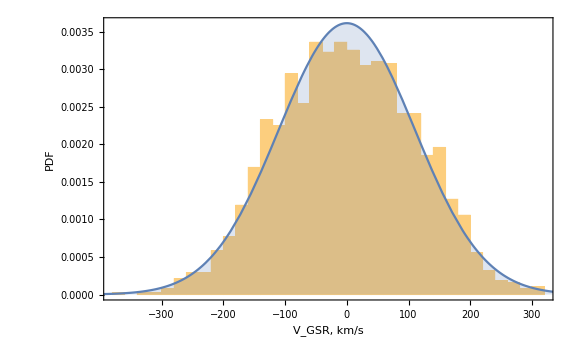

```mathematica
Show[
Histogram[Table[dataxue11select[[i,2]],{i,1,Length[dataxue11select]}],30,"PDF",Frame->True,FrameLabel->{"V_GSR, km/s","PDF"},LabelStyle->Directive[Black,13],ImageSize->Large],
Plot[PDF[NormalDistribution[0,gauss[[2]]],x]//Evaluate,{x,-400,400},Filling->Axis]]
```

Distribution of stars in the sample by the radius

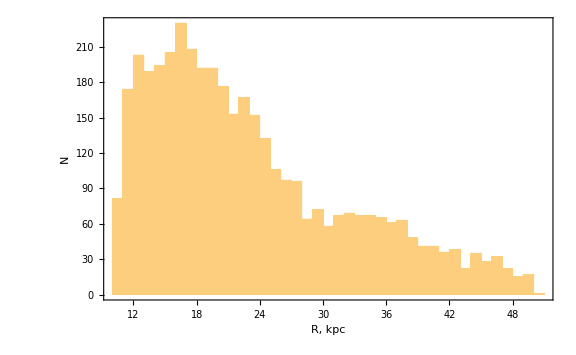

```mathematica
Histogram[Table[dataxue11select[[i,1]],{i,1,Length[dataxue11select]}],30,Frame->True,FrameLabel->{"R, kpc","N"},LabelStyle->Directive[Black,13],ImageSize->Large]
```

Now we bin radially our data and we find the parameters of normal distribution (always centered at 0) in each bin

```mathematica
Clear[n]
standarderrors[data_, dist_, paramlist_, mleRule_] := 
 Block[{len, infmat, cov},
  len = Length[data];
  (* compute negative of expected Fisher information *)
  infmat = -D[LogLikelihood[dist, data], {paramlist, 2}]/len /. mleRule;
  (* invert to get asymptotic covariance for Sqrt[n](theta-theta0) *)
  cov = Inverse[infmat];
  (* standard errors are the Sqrt of diagonal elements divided by sample size *)
  Sqrt[Diagonal[cov]/len]
 ]
(*-----*)
σvel[S_?NumericQ,mydata_]:={
dist = NormalDistribution[n,p];
bins=GatherBy[mydata,Ceiling[First[#],S] &];
(*meanrad if one wnats to use the SD instead of mid of a bin*)
meanrad={};
sdrad={};
disp={};
sterr={};
 For[j=1,j≤Length[bins],j++,
	length=bins[[j]];
	length2=Table[length[[i,2]],{i,1,Length[length]}];


	AppendTo[disp,FindDistributionParameters[Table[bins[[j,i,2]],{i,1,Length[length]}],NormalDistribution[0,p],ParameterEstimator->{"MaximumLikelihood"}]];
	AppendTo[meanrad,Mean[Table[bins[[j,i,1]],{i,1,Length[length]}]]];
 (*   AppendTo[sdrad,StandardDeviation[Table[bins[[j,i,1]],{i,1,Length[length]}]]/(1(*Sqrt[Length[length]]*))];*)
	AppendTo[sterr,standarderrors[length2, dist, {n, p}, disp[[j]]][[2]]];
];



(*];*)

(*Table[{meanrad[[i]],disp[[i,2,2]],sterr[[i]]},{i,1,Length[disp]}]
*)


Table[{(*meanrad[[i]]*)8.+(i-1)(*1*),p/. disp[[i(*,2*)]],sterr[[i]]},{i,1,Length[disp]}]
(*bins*)}
```

```mathematica
finσgsr=Flatten[σvel[1,dataxue11select],1];
```

fitting the exp form function to the binned data

```mathematica
Clear[a]
```

FittedModel[118.169 ⅇ^(-0.00574681 r)]

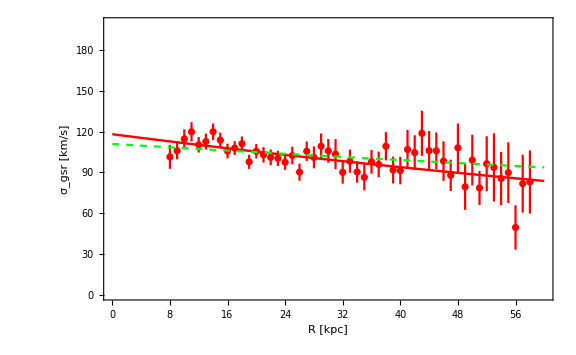

{a→118.169,b→174.01}

{3.04481,31.7865}

```mathematica
n=0;
σxue08[r_]:=111 Exp[-r/354]
σmodel[a_,b_,r_]:=a Exp[-r/b]
errors=Table[finσgsr[[i,3]],{i,1,Length[finσgsr]}];


fit=NonlinearModelFit[Table[{finσgsr[[i,1]],finσgsr[[i,2]]},{i,1,Length[finσgsr]}],{σmodel[a,b,r]},{a,b},r,Weights->1/errors^2,VarianceEstimatorFunction->(1&)]

Show[ErrorListPlot[finσgsr,PlotStyle->Directive[PointSize[0.009],Red],
PlotRange->{{0,60},{0,200}},Frame->True,FrameStyle->Directive[Black,Thickness[0.001],15],
Background->White,FrameTicksStyle -> Directive[RGBColor[0,0,0.26], 13],
LabelStyle->Directive[Black,5.5],FrameLabel->{"R [kpc]","σ_gsr [km/s]"},ImageSize->Large],
Plot[fit[r],{r, 0,60}, PlotRange->{{0,60},{0, 200}}, PlotStyle->Directive[Thickness[0.003],Red]],
Plot[σxue08[r],{r,0,60},PlotStyle->Directive[Dashed,Green]]]
par=fit["BestFitParameters"]
err=fit["ParameterErrors"]
```

Now we translate σ_los to σ_r using the following formula

```mathematica
(*Subscript[σ, los] to Subscript[σ, r]*)
βr={{8,0.6},{9,0.6},{10,0.6},{11,0.7},{12,0.7},{13,0.5},{14,0.2},{15,-0.25},{16,-0.65},{17,-1.1},{18,-0.63},{19,0.26},{20,0.28},{21,-0.14},{22,-0.14},{23,-0.14},{24,0.4},{25,0.4},
{26,0.4},{27,0.4},{28,0.4},{29,0.4},{30.4,0.4},{31,0.4},{32,0.4},{33,0.4},{34,0.4},{35,0.4},{36,0.4},{37,0.4},{38,0.4},{39,0.4},{40.4,0.4},{41,0.4},{42,0.4},{43,0.4},{44,0.4},{45,0.4},
{46,0.4},{47,0.4},{48,0.4},{49,0.4},{50,0.40},{51,0.4},{52,0.4},{53,0.4},{54,0.4},{55,0.4},{56,0.4},{57,0.4},{58,0.4},{59,0.4},{60,0.4},{61,0.4}};

H[r_]:=(r^2+R0^2)/(4 r^2)-((r^2-R0^2)^2)/(8 r^3 R0)Log[Abs[(r+R0)/(r-R0)]]
σr=Table[{finσgsr[[i,1]],finσgsr[[i,2]]/Sqrt[1-βr[[i,2]] H[finσgsr[[i,1]]]]},{i,1,Length[finσgsr]}]

(* functional form for fitting the Subscript[σ, r] profiles, see e.g. Sommer-Larsen et al. 1997 or Kafle et al. 2012*)
(*σmodelf[σ0_,σp_,l_,r0_,r_]:=Sqrt[σ0^2+ σp^2/Pi(Pi/2-ArcTan[(r-r0)/l])]
*)

(*we fit this formula breaking our σgsr into two parts r=<20 || r≥20*)
σmodelf[(*σr0_,*)rσ_,r_]:=145.2(*σr0*) r^rσ
(*σmodelf[σr0_,rσ_,r_]:=σr0 r^rσ*)
(*σmodel=Interpolation[Table[{σr[[i,1]],σr[[i,2]]},{i,1,Length[σr]}]]
*)(*error propogation on Subscript[σ, r]*)
errors1=Table[1/Sqrt[1-βr[[i,2]] H[finσgsr[[i,1]]]] finσgsr[[i,3]],{i,1,Length[finσgsr]}]
fitσr=NonlinearModelFit[Table[{σr[[i,1]],σr[[i,2]]},{i,1
,Length[σr]}],{σmodelf[(*σ0,σp,l,r0,r*)(*σr0,*)rσ,r](*(*,0<rσ<20*),σ0>12,0<σp<200,1<l<4,0<r0<30*)},(*{σ0,σp,l,r0*){(*σr0,*)rσ},r,
Weights->1/Table[errors1[[i]],{i,1,Length[errors1]}]^2,VarianceEstimatorFunction->(1&)]
parσr=fitσr["BestFitParameters"]
```

{{8.,121.305},{9.,122.984},{10.,129.817},{11.,135.647},{12.,122.457},{13.,119.934},{14.,122.535},{15.,111.349},{16.,100.716},{17.,100.457},{18.,106.981},{19.,99.3037},{20.,107.144},{21.,102.314},{22.,100.504},{23.,99.7773},{24.,98.9523},{25.,103.835},{26.,91.331},{27.,106.848},{28.,102.21},{29.,110.395},{30.,106.862},{31.,104.37},{32.,90.8391},{33.,99.0546},{34.,91.0224},{35.,87.0544},{36.,98.4495},{37.,96.5188},{38.,109.947},{39.,92.2553},{40.,91.894},{41.,107.452},{42.,105.1},{43.,119.402},{44.,106.547},{45.,106.384},{46.,98.7425},{47.,88.2178},{48.,108.595},{49.,79.6585},{50.,99.4046},{51.,78.8395},{52.,96.7067},{53.,94.0021},{54.,85.7687},{55.,90.1056},{56.,49.5651},{57.,81.9288},{58.,83.1589}}

{10.5025,7.27437,8.02186,8.0067,6.3232,6.19237,6.2057,5.48877,5.12787,4.7259,5.11333,5.26504,5.40887,5.66437,5.75851,5.56096,5.66519,6.54161,6.40784,7.23486,8.12674,9.54857,8.83258,11.2025,8.43457,8.60203,7.94649,9.75372,8.81758,9.4882,10.4484,9.93798,10.1754,14.4661,12.864,16.6988,14.5333,13.5544,14.6007,11.5889,17.9142,16.9949,18.7228,12.5712,20.3028,25.1954,19.6147,22.4265,16.3729,21.4008,23.3501}

FittedModel[145.2/r^0.107952]

{rσ→-0.107952}

Here is show the fit results to σr from 11 to 20 kpc and from 20 to 58 kpc. The ruslting functions are plotted in black below.

```mathematica
(*11 kpc to 18 kpc*)
σmodelf1[r_]=504. r^-0.56;
(*18 kpc to 58 kpc*)
 σmodelf2[r_]=143. r^-0.11361092318390857;
```

since Kafle et al. 2011 used the same sample  I compare σ_r with their values, I get that the results are not complitely the same. In particular first too point are different by ~20 km/s. I am not sure from where this difference come from, but my guess is that the distances in the sample of Xue et al. 2011 were calibrated by Kafle while I did not do this calibration. Therefore in the farther analysis I am going to exclude
8-10 kpc data and start from 11 kpc.

```mathematica
Kafle12={{7.2,144.8,15.5},{9.9,145.2,11.69},{12.0,139.2,8.4},{14.1,124.8,8.9},{16.1,98.7,12.2},{17.8,104.8,8.3},{19.8,99.8,6.7},{22.1,101.5,6.1},
{24.8,96,6.1},{28.8,101,5.5},{34.7,92.7,6.1},{42.6,103.3,3.8},{55.5,91.1,5.6}};
```

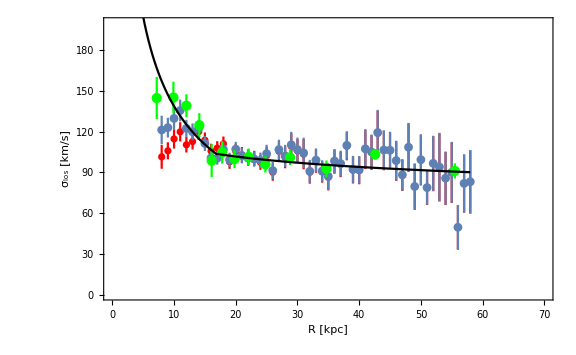

```mathematica
Show[(*ListLogLinearPlot[σmodel[185.5,-0.19,r],{r,0,60},PlotRange->{{0,70},{0,200}}],*)
ErrorListPlot[finσgsr,PlotStyle->Directive[PointSize[0.009],Red],
PlotRange->{{0,70},{0,200}},Frame->True,FrameStyle->Directive[Black,Thickness[0.001],15],
Background->White,FrameTicksStyle -> Directive[RGBColor[0,0,0.26], 13],
LabelStyle->Directive[Black,5.5],FrameLabel->{"R [kpc]","σ_los [km/s]"},ImageSize->Large],ErrorListPlot[Table[{σr[[i,1]], σr[[i,2]],errors1[[i]]},{i,1,Length[σr]}]],(*,
LogLinearPlot[σmodelf[σ0/.parσr[[1]],σp/.parσr[[2]],l/.parσr[[3]],r0/.parσr[[4]],(*94.5,122.3,2.6,13.2,*)r],{r,7,61}]*)(*Plot[fitσr[r],{r, 11,60},

PlotStyle->Directive[Thickness[0.003],Red]],*)ErrorListPlot[Kafle12,PlotStyle->Green],Plot[σmodelf1[r],{r,1,17},PlotStyle->Black],Plot[σmodelf2[r],{r,17,58},PlotStyle->Black](*,
Plot[σxue08[r],{r,5,50}]*)]
```

Here we are going to difine V_circ using the Jeans equation for the spherical model. First, we have to make a set of assumptions:

the number density of halo stellar population follows a broken power low ρ~r^-α. For the inner halo we assume α=2.4 and for the outer α=4.5, we set the broken radius to 19 kpc.

then in order to calculate the derivative of σ_r(r) in the Jeans equation I use the fit fromulas defined above with the broke radius of 18 kpc

the Jeans equation can be written in this form:  V_c^2=-r/(ρ(r))(d[(σ_r(r))^2 ρ(r)]/dr)-2(βσ_r(r))^2     or    V_c^2=-r/(ρ(r))(2σ_r(r)ρ(r)dσ_r/dr+(σ_r(r))^2(dρ(r))/dr)-2(βσ_r(r))^2

then the error propogation from σ_r to V_c can be written in this from δV_c=(∂V_c)/(∂σ_r)δσ_r     or     δV_c=(-r/(ρ(r))(2ρ(r)dσ_r/dr+2σ_r(r)(dρ(r))/dr)-4βσ_r(r))/(√-r/(ρ(r))(2σ_r(r)ρ(r)dσ_r/dr+(σ_r(r))^2(dρ(r))/dr)-2(βσ_r(r))^2)  . In theory we should also add the error on the β estimation, but for now we omitt this.

```mathematica
ρ[r_]=If[r<19, r^-2.4,r^-4.5];
dlnρ[r_]=D[Log[ρ[r]],r];
σrr[r_]=If[r<18, 504 r^-0.56,143. r^-0.11361092318390857];
dlnσ2[r_]=D[Log[σrr[r]^2],r];
derσρ[r_]=D[σrr[r]^2 ρ[r],r];
dσ[r_]=D[σrr[r],r];
dρ[r_]=D[ρ[r],r];
δVc31=Table[{σr[[i,1]],Sqrt[(-σr[[i,1]])/ρ[σr[[i,1]]](2σr[[i,2]]dσ[σr[[i,1]]]ρ[σr[[i,1]]]+σr[[i,2]]^2 dρ[σr[[i,1]]])-2βr[[i,2]] σr[[i,2]]^2],
			((-σr[[i,1]])/ρ[σr[[i,1]]](2dσ[σr[[i,1]]]ρ[σr[[i,1]]]+2σr[[i,2]]dρ[σr[[i,1]]])-4βr[[i,2]]σr[[i,2]])/Sqrt[(-σr[[i,1]])/ρ[σr[[i,1]]](2σr[[i,2]]dσ[σr[[i,1]]]ρ[σr[[i,1]]]+σr[[i,2]]^2 dρ[σr[[i,1]]])-2βr[[i,2]] σr[[i,2]]^2] errors1[[i]]},{i,1,Length[σr]}]
(*δVc32=Table[{σr[[i,1]],Sqrt[(-σr[[i,1]])/ρ[σr[[i,1]]] derσρ[σr[[i,1]]]-2βr[[i,2]] σr[[i,2]]^2]},{i,1,Length[σr]}]
δVc33=Table[{σr[[i,1]],Sqrt[(-σr[[i,1]])/ρ[σr[[i,1]]](2σr[[i,2]]dσ[σr[[i,1]]]ρ[σr[[i,1]]]+σr[[i,2]]^2 dρ[σr[[i,1]]])-2βr[[i,2]] σr[[i,2]]^2]},{i,1,Length[σr]}]*)
```

{{8.,197.554,24.8427},{9.,196.042,17.0719},{10.,201.011,18.638},{11.,195.942,17.1086},{12.,179.405,13.5798},{13.,190.359,15.2905},{14.,214.029,17.9451},{15.,223.049,18.941},{16.,222.635,19.9184},{17.,240.883,20.3981},{18.,210.694,19.573},{19.,203.855,21.016},{20.,218.42,21.4802},{21.,228.89,24.7748},{22.,224.903,25.1867},{23.,223.289,24.3227},{24.,196.137,21.8043},{25.,205.506,25.1763},{26.,181.418,24.6642},{27.,211.255,27.8436},{28.,202.307,31.277},{29.,218.034,36.7469},{30.,211.213,33.9922},{31.,206.399,43.1133},{32.,180.34,32.4646},{33.,196.13,33.1065},{34.,180.654,30.5858},{35.,173.,37.5432},{36.,194.912,33.936},{37.,191.179,36.5175},{38.,217.003,40.2093},{39.,182.942,38.2499},{40.,182.231,39.1637},{41.,212.155,55.6713},{42.,207.614,49.5062},{43.,235.118,64.2593},{44.,210.37,55.9298},{45.,210.042,52.1626},{46.,195.325,56.192},{47.,175.059,44.6052},{48.,214.258,68.9395},{49.,158.561,65.4188},{50.,196.549,72.0554},{51.,156.961,48.3912},{52.,191.335,78.1372},{53.,186.119,96.9691},{54.,170.263,75.4967},{55.,178.598,86.3152},{56.,100.545,63.0767},{57.,162.841,82.3748},{58.,165.198,89.8764}}

Below we plot the resulting V_c and compare in with the Galkin compilation not binned/binned. Additionally, we plot the RC that was provided by Huang et al 2016

```mathematica
dataHuang16={{4.6,231.24,7.,"H~{\\sc","i}"},{5.08,230.46,7.,"H~{\\sc","i}"},{5.58,230.01,7.,"H~{\\sc","i}"},{6.1,239.61,7.,"H~{\\sc","i}"},{6.57,246.27,7.,"H~{\\sc","i}"},{7.07,243.49,7.,"H~{\\sc","i}"},{7.58,242.71,7.,"H~{\\sc","i}"},{8.04,243.23,7.,"H~{\\sc","i}"},{8.34,239.89,5.92,"MRCG"},{8.65,237.26,6.29,"MRCG"},{9.2,235.3,5.6,"MRCG"},{9.62,230.99,5.49,"MRCG"},{10.09,228.41,5.62,"MRCG"},{10.58,224.26,5.87,"MRCG"},{11.09,224.94,7.02,"MRCG"},{11.58,233.57,7.65,"MRCG"},{12.07,240.02,6.17,"MRCG"},{12.73,242.21,8.64,"MRCG"},{13.72,261.78,14.89,"MRCG"},{14.95,259.26,30.84,"MRCG"},{15.52,268.57,49.67,"HKG"},{16.55,261.17,50.91,"HKG"},{17.56,240.66,49.91,"HKG\\\\"},{18.54,215.31,24.8,"HKG\\\\"},{19.5,214.99,24.42,"HKG\\\\"},{21.25,251.68,19.5,"HKG\\\\"},{23.78,259.65,19.62,"HKG\\\\"},{26.22,242.02,18.66,"HKG\\\\"},{28.71,224.11,16.97,"HKG\\\\"},{31.29,211.2,16.43,"HKG\\\\"},{33.73,217.93,17.66,"HKG\\\\"},{36.19,219.33,18.44,"HKG\\\\"},{38.73,213.31,17.29,"HKG\\\\"},{41.25,200.05,17.72,"HKG\\\\"},{43.93,190.15,18.65,"HKG\\\\"},{46.43,198.95,20.7,"HKG\\\\"},{48.71,192.91,19.24,"HKG\\\\"},{51.56,198.9,21.74,"HKG\\\\"},{57.03,185.88,21.56,"HKG\\\\"},{62.55,173.89,22.87,"HKG\\\\"},{69.47,196.36,25.89,"HKG\\\\"},{79.27,175.05,22.71,"HKG\\\\"},{98.97,147.72,23.55,"HKG\\\\"}};
```

```mathematica
dataGalkin=Import["/Users/ekarukes/Dropbox/MWRC/data/RC/vcdataWOoutliersR8v230.dat","Table"]//Sort;
binnedGalkin={{3.32780806773708,212.44595577329443,10.367790020039694,0.40907062053535026},{5.0452292015004385,225.40360546959272,13.381184885929523,0.5645460815998811},
{7.124358065497504,234.96793803312232,18.003628976887263,0.5911234590717399},{8.861903240727989,226.1913788502476,31.586030619313245,0.6119933090201194},
{10.805709453288618,225.83214994159366,26.19240044831798,0.5616616912882052},{12.875909724493592,237.1990447834615,41.768542015438065,0.5955395760742419},
{14.904002989996775,242.2263492711935,84.53638557583633,0.5162463472764224},{16.968695566745453,247.4741517991818,66.91515083434149,0.6322390905256741},
{18.768922325766667,261.1855677423334,41.7612826546036,0.6633460421238743},{20.966046924275,256.15695909075,49.67057342398745,0.7383528033329259},
{22.1702878065,157.376404322,157.376404322,22.1702878065}};
```

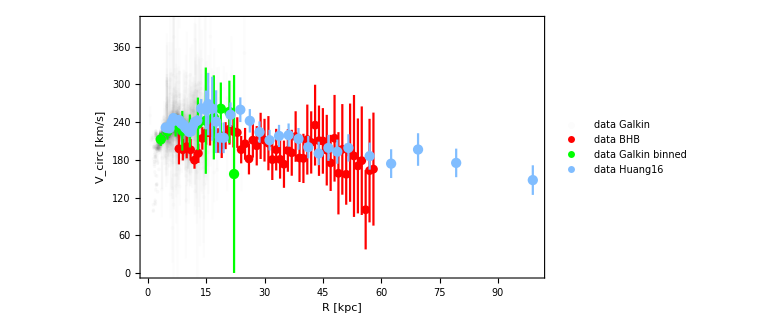

```mathematica
Show[ErrorListPlot[Table[{dataGalkin[[i,1]],dataGalkin[[i,3]],dataGalkin[[i,4]]},{i,1,Length[dataGalkin]}],PlotStyle->Directive[Gray,Opacity[0.025]],
PlotRange->{{0,100},{0,400}},PlotLegends->Placed[LineLegend[{"data Galkin"},LabelStyle->{Gray,17},LegendLayout->"Row"],{0.8,0.05}],Frame->True,AspectRatio->1/1.75,FrameStyle->Directive[Black,Thickness[0.001],15],Background->White,
FrameTicksStyle -> Directive[RGBColor[0,0,0.26], 13],LabelStyle->Directive[Black,5.5],FrameLabel->{"R [kpc]","V_circ [km/s]"},ImageSize->Large],
	ErrorListPlot[{δVc31(*δVc32*)},PlotStyle->{Red},PlotLegends->Placed[LineLegend[{"data BHB"},LabelStyle->{Red,17},LegendLayout->"Row"],{0.8,0.1}]],
	ErrorListPlot[Table[{binnedGalkin[[i,1]],binnedGalkin[[i,2]],binnedGalkin[[i,3]]},{i,1,Length[binnedGalkin]}],PlotStyle->Green,PlotLegends->Placed[LineLegend[{"data Galkin binned"},LabelStyle->{Green,17},LegendLayout->"Row"],{0.8,0.15}]],
	ErrorListPlot[Table[{dataHuang16[[i,1]],dataHuang16[[i,2]],dataHuang16[[i,3]]},{i,1,Length[dataHuang16]}],PlotStyle->RGBColor[0.5,0.74,1],PlotLegends->Placed[LineLegend[{"data Huang16"},LabelStyle->{RGBColor[0.5,0.74,1],17},LegendLayout->"Row"],{0.8,0.2}]]]
```